## Dynamics of a repressor and its target

Moving beyond a single, unregulated gene, the next simplest system we can construct consists of two genes, one of which encodes a protein that represses the transcription of the other. If p_1 is a repressor of gene 2, then a simple model of the rate of transcription from gene 2 would be:

S_2(p_1)=mSynth_2/(1+repStrength_(1,2)p_1)

where S_2 is the transcription rate from gene 2, which is a function of the concentration of the repressor, p_1.

First, let's try exploring the dynamics of this system by symbolic integration. In all, we have a system of four differential equations, one for each mRNA and one for each protein, plus four algebraic equations naming the concentrations of the proteins and mRNAs at time zero as p1Init, p2Init, m1Init, and m2Init. Let’s define the variable diffEqsRepTarg to be these equations.

```mathematica
diffEqsRepTarg=
{m1'[t]==synthRt1 -mDeg1* m1[t],p1'[t]==transRtC1*m1[t]-pDeg1*p1[t],m2'[t]==v2/(1+repStrength12 *p1[t])-mDeg2* m2[t],p2'[t]==transRtC2*m2[t]-pDeg2*p2[t], m1[0]==m1Init, m2[0]==m2Init, p1[0]==p1Init, p2[0]==p2Init}
```

```mathematica
{m1'[t]==synthRt1-mDeg1 m1[t],p1'[t]==transRtC1 m1[t]-pDeg1 p1[t],m2'[t]==-mDeg2 m2[t]+v2/(1+repStrength12 p1[t]),p2'[t]==transRtC2 m2[t]-pDeg2 p2[t],m1[0]==m1Init,m2[0]==m2Init,p1[0]==p1Init,p2[0]==p2Init}
```

```mathematica
repTargSoln1=DSolve[diffEqsRepTarg,{m1,m2,p1,p2},t]
```

$Aborted

I let this run for a while with no result. Eventually, I replaced all the constants by numbers and ran it again for at least 10 minutes. Eventually I got a solution, but it was implicit, meaning that it contained indefinite integrals. This result was difficult to understand and it’s  not clear how useful it would be, compared just integrating original differential equations numerically with NDSolve. To try that, we’ll need to replace all the constants by numbers:

```mathematica
synthRt1=1; mDeg1=1;mDeg2=1;transRtC1=1;transRtC2=1;pDeg1=1;pDeg2=1;mDeg2=1;m1Init=0;m2Init=0;p1Init=0;p2Init=0;v2=1; repStrength12=1;
```

The system now looks like this:

```mathematica
diffEqsRepTarg
```

{m1'[t]==1-m1[t],p1'[t]==m1[t]-p1[t],m2'[t]==-m2[t]+1/(1+p1[t]),p2'[t]==m2[t]-p2[t],m1[0]==0,m2[0]==0,p1[0]==0,p2[0]==0}

The other change is that, instead of just specifying t as the variable with respect to which we want to integrate, we must also specify the start and end of the time interval over which we want to integrate.

```mathematica
NDSolve[diffEqsRepTarg,{m1,m2,p1,p2},{t,0,40}]
```

{{m1→InterpolatingFunction[{{0., 40.}}, <>],m2→InterpolatingFunction[{{0., 40.}}, <>],p1→InterpolatingFunction[{{0., 40.}}, <>],p2→InterpolatingFunction[{{0., 40.}}, <>]}}

The value returned is a list of solutions (one solution, in this case) each of which is a list of rules. Each rule defines the solution functions as interpolating functions, which is to say functions that have defined values at certain points (in this case certain times) and get the values at intermediate points by interpolating between the defined points.

This time let’s grab the first (and only) solution from the list of solutions.

```mathematica
repTargSoln1N=NDSolve[diffEqsRepTarg,{m1,m2,p1,p2},{t,0,40}][[1]]
```

{m1→InterpolatingFunction[{{0., 40.}}, <>],m2→InterpolatingFunction[{{0., 40.}}, <>],p1→InterpolatingFunction[{{0., 40.}}, <>],p2→InterpolatingFunction[{{0., 40.}}, <>]}

We can plot these functions and they will look as though they were continuous:

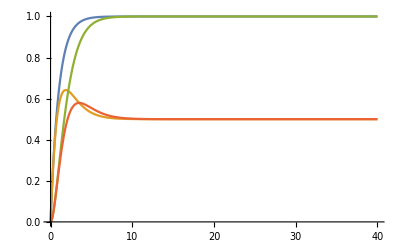

```mathematica
Plot[Evaluate[{m1[t], m2[t],p1[t],p2[t]}/.repTargSoln1N],{t,0,40},PlotRange->All]
```

Cool! But that’s just for one particular set of parameters. Let’s try to wrap this whole thing in a function to which we can pass in the parameters as arguments. First, though, let’s clear the parameter symbols of the values that have been assigned to them, so we can make sure we’re starting with a clean slate.

```mathematica
Clear[synthRt1, mDeg1,mDeg2,transRtC1,transRtC2,pDeg1,pDeg2,m1Init,m2Init,p1Init,p2Init,v2, repStrength12]
```

```mathematica
nSolveRepTarg[synthRt1_,mDeg1_,mDeg2_,transRtC1_,transRtC2_,pDeg1_,pDeg2_,m1Init_,m2Init_,p1Init_,p2Init_,v2_,repStrength12_]:=
Module[
{soln1=NDSolve[{
m1'[t]==synthRt1 -mDeg1* m1[t],
p1'[t]==transRtC1*m1[t]-pDeg1*p1[t],m2'[t]==v2/(1+repStrength12 *p1[t])-mDeg2* m2[t],p2'[t]==transRtC2*m2[t]-pDeg2*p2[t], 
m1[0]==m1Init, m2[0]==m2Init, p1[0]==p1Init, p2[0]==p2Init},{m1,m2,p1,p2},{t,0,40}][[1]]},
Plot[Evaluate[{m1[t], m2[t],p1[t],p2[t]}/.soln1],{t,0,40},PlotRange->All]]
```

Now evaluating this function with parameters as arguments should produce a plot of the protein and RNA concentrations as a function of time, for those parameters.

```mathematica
nSolveRepTarg[1,1,1,1,1,1,1,0,0,0,0,1,1]
```

We need the Evaluate so the list of replacement rules soln1 will be applied -- normally, Plot treats it’s first argument as a formal expression to be evaluated separately at each point along the x axis. Now we can wrap this in Manipulate so we can play with the parameters and see the effects.

```mathematica
Manipulate[nSolveRepTarg[synthRt1,mDeg1,mDeg2,transRtC1,transRtC2,pDeg1,pDeg2,0.,0.,0.,0.,synthRt2,repStrength12],{synthRt1, 0.,1.},{mDeg1, 0.001,1.},{transRtC1, 0.,1.},{pDeg1, 0.001,1.},{repStrength12, 0.,20.},{synthRt2, 0.,1.},{mDeg2, 0.001,1.},{transRtC2, 0.,1.},{pDeg2, 0.001,1.}]
```

##### Exercise: Reparameterizing in terms of half-time and equilibrium concentration

As we saw earlier, the rate at which a molecule’s concentration gets half way to equilibrium depends on its degradation rate constant. We could call this time the “halftime” or “halflife” of the molecule. We also saw, by taking the limits of the concentrations as time grows without bound, that those limits -- i.e. the equilibrium concentrations -- depend on both the degradation rate and the synthesis rate in a very simple way. Here, your task is to set up a Manipulate panel for the system we have just been studying, but where the sliders control the half-lives and equilibrium concentrations directly. To do that, you have to use the equations describing relations between the old parameters (e.g. synthRt1) and the new ones (e.g. p1EqConc) to solve for the old parameters in terms of the new ones (e.g. what is synthRt1, given that you know the various equilibrium concentrations and half-lives?). Now, you will write a function that takes in half-lives and equilibrium concentrations, calculates the values of the old parameters (e.g.  synthRt1), and calls nSolveRepTarg with the old parameters. Then plot this new function from within a Manipulate where the half lives and equilibrium constants are controlled by sliders. The only “old” parameter that will still be controlled directly from the sliders is repStrength12. Be careful to set the ranges for your sliders so you don’t end up dividing by zero.

When you’re done, you should be able to control the halflives without changing the equilibrium concentrations. If you make the halflife range relatively small, compared to the horizontal axis of the graph, you should see almost no change in the height of the lines at the right of the graph when you change the half-life. Of course, if the halflives get too long relative to the graph, your concentrations won’t be near equilibrium on your graph. One way to fix this would be to make the range of the horizontal axis on the graph a certain number of times (e.g 5 times) the maximum halflife defined by the sliders at any given moment. This would ensure that everything is always near equilibrium on the right edge of the graph, however it would have another disadvantage....when changing the largest halflife, the horizontal scale would change creating an apparent change in the shapes of the curves.

You should also be able to change the equilibrium concentrations without affecting the shapes of the curves. And changes to the equilibrium concentration of an mRNA should no longer affect the equilibrium concentration of the protein.

```mathematica
byEqAndHL[m1Eq_,m1HL_,m2Eq_,m2HL_,p1Eq_,p1HL_,p2Eq_,p2HL_,m1Init_,m20_,p10_,p20_,repStr12_]:=Module[{
mDeg1=Log[2]/m1HL,pDeg1=Log[2]/p1HL,mDeg2=Log[2]/m2HL,pDeg2=Log[2]/p2HL,synthRt1=m1Eq*(Log[2]/m1HL),
transRtC1=(Log[2]/p1HL)*p1Eq/m1Eq,
synthRt2=(Log[2]/m2HL) (m1Eq) (1+repStr12*p1Eq),
transRtC2=(Log[2]/p2HL) (p2Eq)/m2Eq},nSolveRepTarg[synthRt1,mDeg1,mDeg2,transRtC1,transRtC2,pDeg1,pDeg2,m1Init,m20,p10,p20,synthRt2,repStr12]]
```

```mathematica
Manipulate[byEqAndHL[m1Eq,m1HL,m2Eq,m2HL,p1Eq,p1HL,p2Eq,p2HL,0.,0.,0.,0.,repStr12],{m1Eq,0.001,20.},{m1HL,0.001,20.},{m2Eq,0.001,20.},{m2HL,0.001,20.},{p1Eq,0.001,20.},{p1HL,0.001,20.},{p2Eq,0.001,20.},{p2HL,0.001,20.},{repStr12,0.001,20.}]
```

##### Exercise: Comparing repression models

[Nothing in 2014. For 2015, put in an exercise using the models from the papers.]

##### Exercise: Numerically integrating a generic system of differential equations

Once we have settled on the forms of our equations, we don’t want to have to type them in again every time we want to change the number of genes . Instead, we want to define a function that can take in parameters for a system of any number of genes repressing one another. This is left as an exercise that is specified in more detail below. However, here is an important hint: instead of using m1, m2, p1, p2 as function names, we can use m[1], m[2], ...,p[1], p[2], .... Making the time dependence explicit gives us, for example, m[1][t], the derivative of which can be indicated by m[1]’[t]. So to programmatically construct a system of ODEs you can use, for example, Table[m[i]’[t]==...,{i, 1, n}, where the three dots indicates the right hand side of your equation.

Below is the outline of a function that takes in vectors (lists) of parameters, constructs a list of symbolic equations from them using the m[i][t] approach, prints the equations, and hands them to NDSolve to solve. For this part, write equations in which the expression of each gene is unregulated, but may be governed by different transcription, translation, and degradation rate constants.

```mathematica
nSolveNoRegVect[synthRtVect_,mDegRtConstVect_,translationRtConstVect_,pDegRtConstVect_]:=Module[{numGenes=Length[synthRtVect],eqns,funs,solns},eqns=Table[{m[i]'[t]==synthRtVect[[i]]-mDegRtConstVect[[i]]*m[i][t],p[i]'[t]==translationRtConstVect[[i]]*m[i][t]-pDegRtConstVect[[i]]*p[i][t],m[i][0]==0,p[i][0]==0},{i,1,numGenes}];
funs=Table[{m[i][t],p[i][t]},{i,1,numGenes}];
Print[eqns];
solns=NDSolve[Flatten[eqns,1],Flatten[funs,1],{t,0,40}];
Plot[Evaluate[Flatten[Table[{m[i][t],p[i][t]},{i,numGenes}],1]/.solns],{t,0,40},PlotRange->All]]
```

Now to see it in action, evaluate the following expression. You should get a list of equations followed by a plot.

{{m[1]'[t]==1-m[1][t],p[1]'[t]==m[1][t]-p[1][t],m[1][0]==0,p[1][0]==0},{m[2]'[t]==1-m[2][t],p[2]'[t]==m[2][t]-p[2][t],m[2][0]==0,p[2][0]==0}}

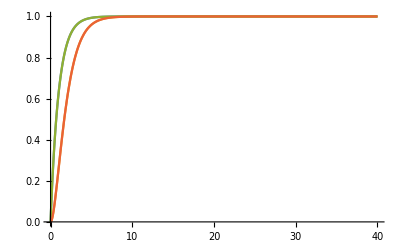

```mathematica
nSolveNoRegVect[{1,1},{1,1},{1,1},{1,1}]
```

##### Exercise: Numerically integrating a system for any number of genes with arbitrary repression parameters

Now do the same thing for a system of proteins that can repress one another according to the simple repression model described above. In addition to all the parameters of the previous exercise, you’ll need a matrix representing the efficiency with which each protein represses the transcription of each other protein.

```mathematica
nSolveRegVect[mSynthRtVect_,repressionMatrix_,mDegRtConstVect_,translationRtConstVect_,pDegRtConstVect_]:=Module[{numGenes=Length[mSynthRtVect],repressionInteractions, newSynthRtVect,eqns,funs,solns},funs=Table[{m[i][t],p[i][t]},{i,1,numGenes}];
repressionInteractions=1+Table[repressionMatrix[[i,j]]*p[i][t],{i,1,numGenes},{j,1,numGenes}];
newSynthRtVect=mSynthRtVect/Times@@repressionInteractions;
eqns=Table[{m[i]'[t]==newSynthRtVect[[i]]-mDegRtConstVect[[i]]*m[i][t],p[i]'[t]==translationRtConstVect[[i]]*m[i][t]-pDegRtConstVect[[i]]*p[i][t],m[i][0]==0,p[i][0]==0},{i,1,numGenes}];
solns=NDSolve[Flatten[eqns,1],Flatten[funs,1],{t,0,40}];
Plot[Evaluate[Flatten[Table[{m[i][t],p[i][t]},{i,numGenes}],1]/.solns],{t,0,40},PlotRange->All,PlotLegends->Automatic]]
```

Now to see it in action, evaluate the following expression. You should get a list of equations followed by a plot. In fact, the plot should be as a plot you made earlier in this note notebook, since the repression coefficient matrix passed in has one of the genes repressing the other.

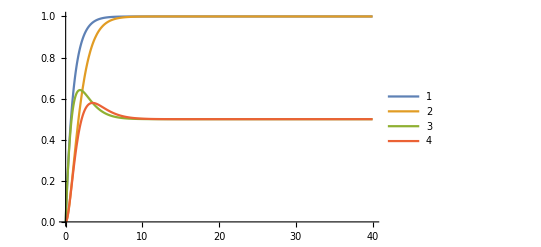

```mathematica
nSolveRegVect[{1,1},{{0,1},{0,0}},{1,1},{1,1},{1,1}]
```

Now write calls to representing a situation where each gene represses itself but not the other, as well as a situation in which each gene represses the other but not itself.

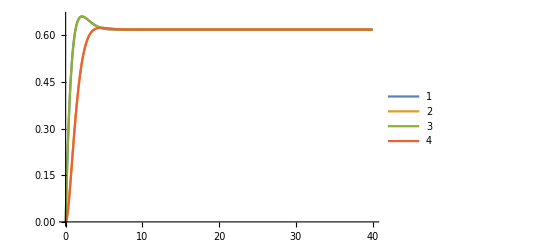

```mathematica
nSolveRegVect[{1,1},{{1,0},{0,1}},{1,1},{1,1},{1,1}]
```

```mathematica
nSolveRegVect[{1,1},{{0,1},{1,0}},{1,1},{1,1},{1,1}]
```

-Graphics-